## Bounds on EDGB Theory From the Overall Posterior of GW150914

```mathematica
dataOverall1=Import[NotebookDirectory[]<>"/overall_post_150914.csv","CSV"];(*Posterior containing cos_theta_inc,luminosity distance,right ascension, declination, m1_det,m2_det,spin_1,spin_2,cos_tilt1,cos_tilt2 respectively.*)
```

```mathematica
dataOverall2=Import[NotebookDirectory[]<>"/beta_150914.csv","CSV"] ; (*PPE beta*)
dataOverall3=Import[NotebookDirectory[]<>"/alpha_150914.csv","CSV"] ;(*PPE alpha*)
```

```mathematica
χ1All=dataOverall1[[All,7]]; (*Dimensionles spin parameter*)
χ2All=dataOverall1[[All,8]];
```

```mathematica
DL=dataOverall1[[All,2]]*10^6*3.261636*tyear/.tyear->3.1536*10^7
```

{4.51425×10^16,6.31727×10^16,5.00873×10^16,3.92708×10^16,5.55192×10^16,2.70936×10^16,4.16762×10^16,16318,5.08785×10^16,3.9558×10^16,5.22933×10^16,3.93816×10^16,5.38142×10^16,3.86166×10^16,4.45333×10^16}
 |  |  |  |

```mathematica
Clear[z]
```

```mathematica
Clear[z1,z2]
```

```mathematica
$Assumptions:=z1<1
```

```mathematica
A=Series[(ωM(1+z1)^3+ωΛ)^(-1/2),{z1,0,1}]//Normal
```

-(3 z1 ωM)/(2 (ωM+ωΛ)^(3/2))+1/(√(ωM+ωΛ))

```mathematica
B=(1+z)/H0 Integrate[A,{z1,0,z}]//Expand
```

-(3 z^2 ωM)/(4 H0 (ωM+ωΛ)^(3/2))-(3 z^3 ωM)/(4 H0 (ωM+ωΛ)^(3/2))+z/(H0 √(ωM+ωΛ))+z^2/(H0 √(ωM+ωΛ))

```mathematica
B2=Series[B,{z,0,2}]//Normal
```

z/(H0 √(ωM+ωΛ))+(z^2 (ωM+4 ωΛ))/(4 H0 (ωM+ωΛ)^(3/2))

```mathematica
Clear[z]
```

```mathematica
z=z/.Solve[B2-Dl==0,z][[2]]
```

(2 H0 (ωM+ωΛ)^(3/2) (-1/(H0 √(ωM+ωΛ))+√(1/(H0^2 (ωM+ωΛ))+(Dl (ωM+4 ωΛ))/(H0 (ωM+ωΛ)^(3/2)))))/(ωM+4 ωΛ)

```mathematica
z2=z/.{Dl->DL,ωM->0.3111,ωΛ->0.6889,α->0,H0->2.2683085*10^-18}
```

{0.0954171,0.130282,0.105138,0.0837063,0.115676,0.0588054,0.0885261,0.114042,16317,0.106683,0.0842835,0.109436,0.083929,0.112384,0.0823902,0.0942106}
 |  |  |  |

```mathematica
m1All=dataOverall1[[All,5]]/(1+z2)*tsolar/.tsolar->4.925491*10^-6 (*Ligo posterior gives mass in detector frame*);
m2All=dataOverall1[[All,6]]/(1+z2)*tsolar/.tsolar->4.925491*10^-6
```

{0.000154056,0.000150252,0.00013417,0.000166077,0.000153064,0.000129181,0.000164308,16319,0.000145104,0.000141122,0.000145081,0.000126583,0.000133266,0.000149862}
 |  |  |  |

```mathematica
ηAll=(m1All*m2All)/(m1All+m2All)^2;
```

```mathematica
βppEAll=1.64485*dataOverall2[[All,1]](*90% upper bound*)
αppEAll=1.64485*dataOverall3[[All,1]](*90% upper bound*)
```

{0.000156332,0.000162373,0.000163574,0.000160379,0.000156647,0.000177039,0.000164105,16319,0.000164342,0.000162673,0.000161889,0.000172832,0.000171786,0.000167056}
 |  |  |  |

{0.0302981,0.0318019,0.0292794,0.0315932,0.0302164,0.0277693,0.0326856,0.0289989,16317,0.0292295,0.0300739,0.0297445,0.0298373,0.0291293,0.0287067,0.0312694}
 |  |  |  |

```mathematica
s1All=2/χ1All^2*(√(1-χ1All^2)-1+χ1All^2);
s2All=2/χ2All^2*(√(1-χ2All^2)-1+χ2All^2);
```

```mathematica
ζphaseAll=Abs[-7168/5*((m1All+m2All)^4*ηAll^(18/5))/(((m1All^2*s2All)-(m2All^2*s1All))^2)*βppEAll] (*Sigma_Zeta from phase corrections.Eqn. 29 of 1809.00259*);
```

```mathematica
ζampAll=Abs[-192/5*((m1All+m2All)^4*ηAll^(18/5))/(((m1All^2*s2All)-(m2All^2*s1All))^2)*αppEAll]; (*Sigma_Zeta from amplitude corrections*)
```

```mathematica
Length[m1All]
```

16332

```mathematica
Length[βppEAll]
```

16332

```mathematica
Mean[ζampAll]
```

36836.2

```mathematica
Mean[ζphaseAll]
```

6983.3

```mathematica
ζAllphaseSelected=Select[ζphaseAll,# <1 &]; (*Datasets that satisfy Zeta<1 where Zeta is found from phase correction. Since the distribution of zeta is Gaussian with zero mean, sigma_zeta<1 and zeta<1 are analogous*)
ζAllampSelected=Select[ζampAll,# <1 &];(*Datasets that satisfy Zeta<1 where Zeta is found from amplitude correction*)
```

```mathematica
Length[ζAllphaseSelected]
```

11390

```mathematica
Length[ζAllampSelected]
```

6261

```mathematica
Mean[ζAllphaseSelected]
```

0.257895

```mathematica
StandardDeviation[ζAllphaseSelected]
```

0.233642

```mathematica
A1=Table[Append[dataOverall1[[i]],ζphaseAll[[i]]],{i,1,Length[dataOverall1]}]
```

{{-0.901839,438.878,1.6919,-1.27538,36.5582,34.2617,0.394141,0.0330915,-0.213274,-0.961184,0.851562},{1},16329,{-0.960167,432.955,7,0.304489,0.180842}}
 |  |  |  |

```mathematica
A2=Table[Append[A1[[i]],ζampAll[[i]]],{i,1,Length[A1]}] (*Contains all the posterior data and sigma_zeta from both phase and amplitude corrections*)
```

{{-0.901839,438.878,1.6919,-1.27538,36.5582,34.2617,0.394141,0.0330915,-0.213274,-0.961184,0.851562,4.42067},16330,{-0.960167,432.955,8,0.180842,0.906687}}
 |  |  |  |

```mathematica
A3=Select[A2,#[[11]]<1&][[All,{1,2,3,4,5,6,7,8,9,10}]] ;(*Data satisfying zeta_phase<1*)
```

```mathematica
A4=Select[A2,#[[12]]<1&][[All,{1,2,3,4,5,6,7,8,9,10,11,12}]](*Data satisfying zeta_amp<1*)
```

{{-0.835255,614.169,2.3996,-1.15619,39.5694,34.4793,0.70691,0.434739,-0.100755,0.415459,0.188078,0.986691},6259,{-0.960167,432.955,8,0.180842,0.906687}}
 |  |  |  |

```mathematica
A4[[All,12]];
```

```mathematica
Length[A3]
```

11390

```mathematica
Length[A4]
```

6261

```mathematica
Select[A4[[All,11]],#>1&]  (*Proves that all 46872 data with zeta_amp<1 also satisfies zeta_phase<1*)
```

{}

```mathematica
Mean[ζAllampSelected]
```

0.470722

```mathematica
SqrtαEDGBamp=((ζampAll*(m1All+m2All)^4)/(16*π))^(1/4)*3*10^5(*square root of alpha_EDGB (in km) from the amplitdue corrections of all data*)
SqrtαEDGBphase=((ζphaseAll*(m1All+m2All)^4)/(16*π))^(1/4)*3*10^5(*square root of alpha_EDGB from the phase corrections of all data*)
```

{52.0237,36.2351,26.4251,269.33,66.4337,21.3989,73.8615,31.0243,16316,45.1874,26.2662,31.2733,30.9734,32.4533,20.3314,24.1399,36.9204}
 |  |  |  |

{34.4654,23.9425,17.8578,177.704,44.0639,14.9466,48.5997,20.9147,16316,30.5012,17.7206,21.0178,20.8204,21.7719,13.9481,16.5963,24.6732}
 |  |  |  |

```mathematica
Mean[SqrtαEDGBamp] (*just a rough estimate for sanity check. This does not give a statistically meaningful bound*)
```

59.2173

```mathematica
Mean[SqrtαEDGBphase]
```

39.305

```mathematica
tsolar=4.925491*10^-6
```

4.92549×10^-6

```mathematica
SqrtαEDGBphaseSelected=((A4[[All,11]]*(A4[[All,5]]*tsolar+A4[[All,6]]*tsolar)^4)/(16*π))^(1/4)*3*10^5 ;(*square root of alpha_EDGB from phase correction of the data satisfying zeta_phase<1*)
```

```mathematica
SqrtαEDGBampSelected=((A4[[All,12]]*(A4[[All,5]]*tsolar+A4[[All,6]]*tsolar)^4)/(16*π))^(1/4)*3*10^5 ;(*square root of alpha from amplitude correction of the data satisfying zeta_amp<1*)
```

```mathematica
Mean[SqrtαEDGBphaseSelected]
```

21.6435

```mathematica
Mean[SqrtαEDGBampSelected]
```

32.1641

(α^2)_EDGB from phase correction:

```mathematica
LogSquaredαPhase=Log[SqrtαEDGBphase^4] (*This is Log of sigma_(alpha^2)*)
```

{14.1598,12.7026,11.5298,20.7205,15.1426,10.8179,15.5345,12.1618,16316,13.6711,11.4989,12.1815,12.1437,12.3225,10.5414,11.2367,12.8229}
 |  |  |  |

```mathematica
MaxLogSquaredαPhase=Max[LogSquaredαPhase]
```

32.5136

```mathematica
MinLogSquaredαPhase=Min[LogSquaredαPhase]
```

9.59186

```mathematica
𝒟logα=HistogramDistribution[LogSquaredαPhase] ;
```

```mathematica
pslogαPhase=PDF[𝒟logα,x];
```

```mathematica
Histogram[LogSquaredαPhase];
```

```mathematica
fun1αphase[x_,y_]=1/(√(2*π)*Exp[y])*Exp[-x^2/(2Exp[2*y])] (*P(α^2|Subscript[σ, α^2])*)
```

(ⅇ^(-1/2 ⅇ^(-2 y) x^2-y))/(√(2 π))

```mathematica
αSampleLog=Prepend[10^Range[-7,15,0.1],0];(*Sample Subscript[σ, α^2] for integration. I decided to include 0 in the sample*)
```

```mathematica
fun1αphaseTable[y_]=Table[{αSampleLog[[i]],fun1αphase[αSampleLog[[i]],y]},{i,1,Length[αSampleLog]}]; (*Table for fun1αphase*)
```

```mathematica
αPhaseMC[x_]=pslogαPhase;
```

```mathematica
αPhaseMC[4]
```

0.

```mathematica
αPhaseMC[32]
```

0.0000612295

```mathematica
αMCSample=Range[3.5,35,1.2];
```

```mathematica
αMCTable=Table[{αMCSample[[i]],αPhaseMC[αMCSample[[i]]]},{i,1,Length[αMCSample]}];
```

```mathematica
αMCTableInterp=Interpolation[αMCTable];
```

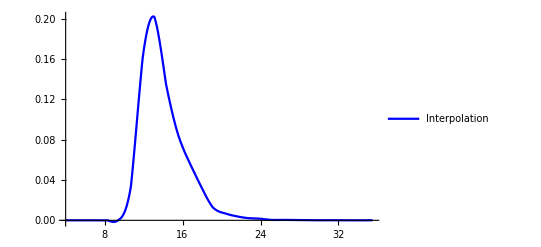

```mathematica
plotαMCTableInterp=Plot[αMCTableInterp[x],{x,4,35.5},PlotStyle->Blue,PlotLegends->{"Interpolation"},PlotRange->All]
```

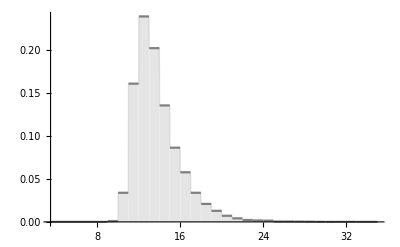

```mathematica
plot5=Plot[αPhaseMC[x],{x,3.5,35},Filling->Axis,PlotStyle->Gray,PlotRange->All]
```

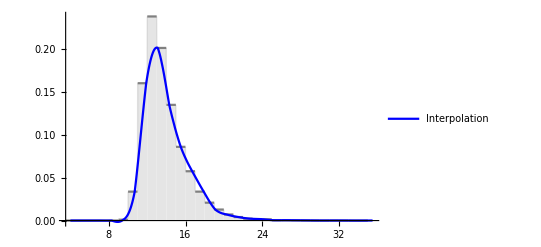

```mathematica
Show[plot5,plotαMCTableInterp] (*Interpolation matches the actual pdf of monte-carlo*)
```

```mathematica
αFinalPDFPhaseLog=Table[{fun1αphaseTable[y][[i,1]],NIntegrate[fun1αphaseTable[y][[i,2]]αMCTableInterp[y],{y,MinLogSquaredαPhase,MaxLogSquaredαPhase}]},{i,1,Length[fun1αphaseTable[y]]}];
```

```mathematica
αFinalPDFPhaseInterpLog=Interpolation[αFinalPDFPhaseLog];
```

```mathematica
αNormalization=NIntegrate[αFinalPDFPhaseInterpLog[x],{x,0,10^15}]
```

0.443514

```mathematica
αFinalPDFPhaseLogNorm=Table[{αFinalPDFPhaseLog[[i,1]],αFinalPDFPhaseLog[[i,2]]/αNormalization},{i,1,Length[αFinalPDFPhaseLog]}];
```

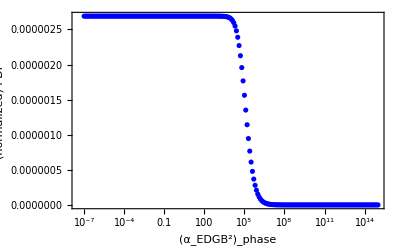

```mathematica
plotαFinalPDFPhaseLogNorm=ListLogLinearPlot[{αFinalPDFPhaseLogNorm},PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue,Red},FrameLabel->{"(α_EDGB^2)_phase","(normalized) PDF"}]
```

```mathematica
αFinalPDFPhaseInterpLogNorm=Interpolation[αFinalPDFPhaseLogNorm];
```

```mathematica
αFinalCDFPhaseNorm=Table[{αSampleLog[[i]],NIntegrate[αFinalPDFPhaseInterpLogNorm[x],{x,0,αSampleLog[[i]]}]},{i,1,Length[αSampleLog]}];
```

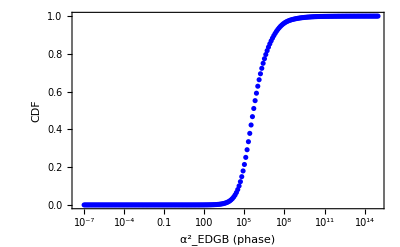

```mathematica
ListLogLinearPlot[αFinalCDFPhaseNorm,PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue},FrameLabel->{"α^2_EDGB (phase)","CDF"}]
```

```mathematica
αFinalCDFPhaseNormInterp=Interpolation[αFinalCDFPhaseNorm];
```

```mathematica
αSquared90CLphase=x/.FindRoot[αFinalCDFPhaseNormInterp[x]==0.9,{x,100}] (*90% CL of Subscript[α^2, EDGB] from phase correction *)
```

1.69052×10^7

```mathematica
√√αSquared90CLphase//N
```

64.1217

```mathematica
Subscript[α^2, EDGB] from amplitude correction:
```

```mathematica
LogSquaredαamp=Log[SqrtαEDGBamp^4]
```

{15.8068,14.3601,13.0973,22.3838,16.7848,12.2534,17.2088,13.7391,16316,15.2433,13.0731,13.7711,13.7325,13.9192,12.0487,12.7355,14.4351}
 |  |  |  |

```mathematica
MaxLogSquaredαamp=Max[LogSquaredαamp]
```

34.1823

```mathematica
MinLogSquaredαamp=Min[LogSquaredαamp]
```

11.1139

```mathematica
𝒟logαamp=HistogramDistribution[LogSquaredαamp] ;
```

```mathematica
pslogαamp=PDF[𝒟logαamp,x];
```

```mathematica
Histogram[LogSquaredαamp];
```

```mathematica
αampMC[x_]=pslogαamp;
```

```mathematica
αampMC[34]
```

0.0000612295

```mathematica
αampMC[4]
```

0.

```mathematica
αMCSampleamp=Range[9,35,1.09];
```

```mathematica
αMCTableamp=Table[{αMCSampleamp[[i]],αampMC[αMCSampleamp[[i]]]},{i,1,Length[αMCSampleamp]}];
```

```mathematica
αMCTableInterpamp=Interpolation[αMCTableamp];
```

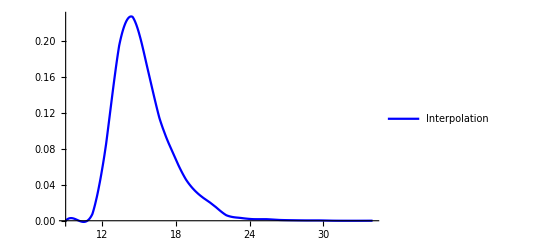

```mathematica
plotαMCTableInterpamp=Plot[αMCTableInterpamp[x],{x,9,34},PlotStyle->Blue,PlotLegends->{"Interpolation"},PlotRange->All]
```

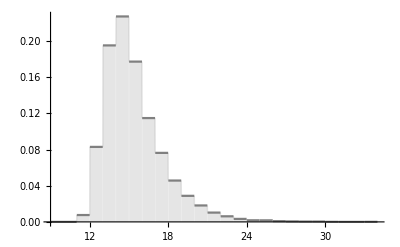

```mathematica
plot6=Plot[αampMC[x],{x,9,34},Filling->Axis,PlotStyle->Gray,PlotRange->All]
```

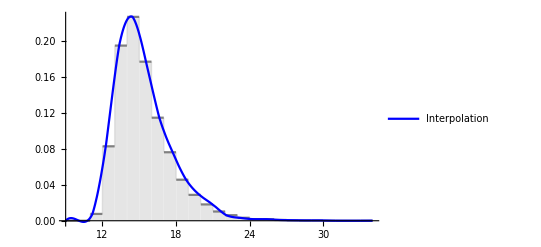

```mathematica
Show[plot6,plotαMCTableInterpamp]
```

```mathematica
αSampleLogamp=Prepend[10^Range[-7,15,0.1],0];
```

```mathematica
fun1αamp[x_,y_]=1/(√(2*π)*Exp[y])*Exp[-x^2/(2Exp[2*y])];
```

```mathematica
fun1αampTable[y_]=Table[{αSampleLogamp[[i]],fun1αphase[αSampleLogamp[[i]],y]},{i,1,Length[αSampleLogamp]}];
```

```mathematica
αFinalPDFampLog=Table[{fun1αampTable[y][[i,1]],NIntegrate[fun1αampTable[y][[i,2]]αMCTableInterpamp[y],{y,MinLogSquaredαamp,MaxLogSquaredαPhase}]},{i,1,Length[fun1αampTable[y]]}];
```

```mathematica
αFinalPDFampInterpLog=Interpolation[αFinalPDFampLog]
```

InterpolatingFunction[…]

```mathematica
αNormalizationamp=NIntegrate[αFinalPDFampInterpLog[x],{x,0,10^15}]
```

0.538797

```mathematica
αFinalPDFampLogNorm=Table[{αFinalPDFampLog[[i,1]],αFinalPDFampLog[[i,2]]/αNormalizationamp},{i,1,Length[αFinalPDFampLog]}];
```

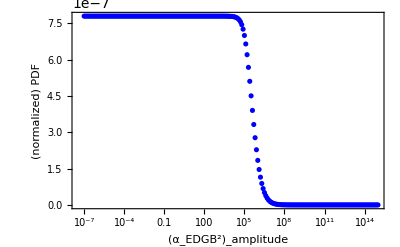

```mathematica
plotαFinalPDFampLogNorm=ListLogLinearPlot[{αFinalPDFampLogNorm},PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue,Red},FrameLabel->{"(α_EDGB^2)_amplitude","(normalized) PDF"}]
```

```mathematica
αFinalPDFampInterpLogNorm=Interpolation[αFinalPDFampLogNorm];
```

```mathematica
αFinalCDFampNorm=Table[{αSampleLogamp[[i]],NIntegrate[αFinalPDFampInterpLogNorm[x],{x,0,αSampleLogamp[[i]]}]},{i,1,Length[αSampleLogamp]}];
```

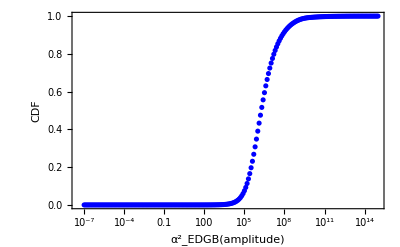

```mathematica
ListLogLinearPlot[αFinalCDFampNorm,PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue},FrameLabel->{"α^2_EDGB(amplitude)","CDF"}]
```

```mathematica
αFinalCDFampNormInterp=Interpolation[αFinalCDFampNorm];
```

```mathematica
αSquared90CLamp=x/.FindRoot[αFinalCDFampNormInterp[x]==0.9,{x,1000}](*90% CL of Subscript[α^2, EDGB] from phase correction *)
```

6.91959×10^7

```mathematica
√√αSquared90CLamp
```

91.2053

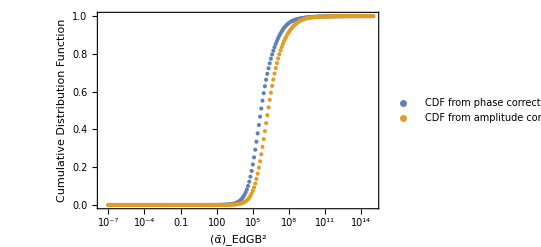

```mathematica
PlotCDFComparison=ListLogLinearPlot[{αFinalCDFPhaseNorm,αFinalCDFampNorm},PlotRange->All,TicksStyle->Directive["Label",14],AxesLabel->{nPN,Subscript[σ, α]},PlotLegends->{Placed[LineLegend[{"CDF from phase correction  ","CDF from amplitude correction"},LabelStyle->{FontSize->5},LegendMarkerSize->10,LegendMargins->0,LegendFunction->"Frame"],{Left,Top}]},FrameLabel->{"(ᾱ)_EdGB^2","Cumulative Distribution Function"},Frame->True] (*Shows that indeed for GW150914, the amplitude and phase corrections are comparable*)
```

## ζ from phase correction

### 2D Gaussian, ζ samples

```mathematica
𝒟log=HistogramDistribution[Log[ζphaseAll]] (*simga_zeta from log of phase correction from monte-carlo. If we use the distribution of ζ, the pdf we get looks almost rectangular. That is why we are using the log[sigma_zeta]. We can compare their shapes from following two histograms *)
```

DataDistribution[…]

```mathematica
Histogram[Log[ζphaseAll]];
```

```mathematica
Histogram[ζphaseAll];
```

```mathematica
ps1=PDF[𝒟log,x];
```

```mathematica
ps2[x]=ps1;
```

```mathematica
plottest2=Plot[ps2[x],{x,Log[Min[ζphaseAll]],Log[Max[ζphaseAll]]},Filling->Axis,PlotStyle->Gray,PlotRange->All];
```

```mathematica
zeta1=ListLinePlot[{{0,0},{0,0.25}},PlotStyle->Red];
```

```mathematica
Show[plottest2,zeta1,Frame->True,PlotRange->All] ;(*Shows how much of the area under the curve satisfies zeta<1 from phase correction*)
```

```mathematica
Integrate[ps2[x],{x,Log[Min[ζphaseAll]],Log[Max[ζphaseAll]]}]
```

0.99934

```mathematica
Integrate[ps2[x],{x,-Infinity,Infinity}]
```

1.

```mathematica
Integrate[ps2[x],{x,Log[Min[ζphaseAll]],0}]/Integrate[ps2[x],{x,Log[Min[ζphaseAll]],Log[Max[ζphaseAll]]}]*100 (*81% area under the curve satisfies zeta<1 from phase correction*)
```

69.7256

```mathematica
MaxLogζphase=Log[Max[ζphaseAll]]
```

18.144

```mathematica
MinLogζphase=Log[Min[ζphaseAll]]
```

-4.87437

```mathematica
fun1kent[x_,y_]=1/(√(2*π) Exp[y])*Exp[-x^2/(2Exp[2y])]
```

(ⅇ^(-1/2 ⅇ^(-2 y) x^2-y))/(√(2 π))

ζ sample

```mathematica
ζSampleLog=Prepend[10^Range[-5,6,0.1],0];
```

Creating a table for fun1Kent[x,y] at each ζ sample for x

```mathematica
fun1TableLog[y_]=Table[{ζSampleLog[[i]],fun1kent[ζSampleLog[[i]],y]},{i,1,Length[ζSampleLog]}];
```

```mathematica
ζMC[x_]=ps1;
```

```mathematica
ζMC[-6.5]
```

0.

```mathematica
ζMC[18]
```

0.0000612295

ζ sample for creating an interpolation function for the MC prob distribution
Since ζ > 0, I only consider positive ζ

```mathematica
ζMCSample=Range[-9.5,18,1];
```

creating a table for the MC distribution at each sample ζ

```mathematica
ζMCTable=Table[{ζMCSample[[i]],ζMC[ζMCSample[[i]]]},{i,1,Length[ζMCSample]}];
```

creating an interpolation function

```mathematica
ζMCTableInterp=Interpolation[ζMCTable];
```

Plot

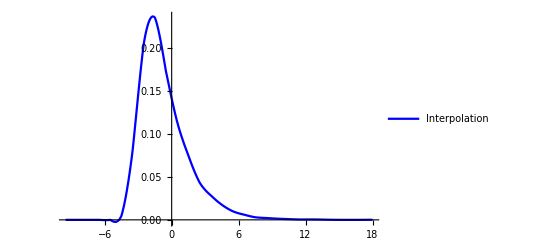

```mathematica
plotζMCTableInterp=Plot[ζMCTableInterp[x],{x,-9.5,18},PlotStyle->Blue,PlotLegends->{"Interpolation"}]
```

Comparison with the actual distribution

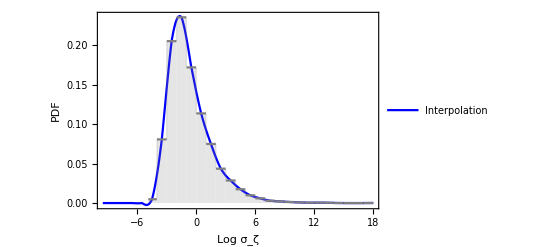

```mathematica
Show[plotζMCTableInterp,plottest2,Frame->True,FrameLabel->{"Log σ_ζ","PDF"}]
```

```mathematica
ζFinalPDFPhaseLog=Table[{fun1TableLog[y][[i,1]],NIntegrate[fun1TableLog[y][[i,2]]ζMCTableInterp[y],{y,MinLogζphase,MaxLogζphase}]},{i,1,Length[fun1TableLog[y]]}];
```

#### Normalized Distribution

Interpolation

```mathematica
ζFinalPDFPhaseInterpLog=Interpolation[ζFinalPDFPhaseLog];
```

Normalization

```mathematica
Normalization=NIntegrate[ζFinalPDFPhaseInterpLog[x],{x,0,10^6}]
```

0.500003

Normalized distribution

```mathematica
ζFinalPDFPhaseLogNorm=Table[{ζFinalPDFPhaseLog[[i,1]],ζFinalPDFPhaseLog[[i,2]]/Normalization},{i,1,Length[ζFinalPDFPhaseLog]}];
```

Plot

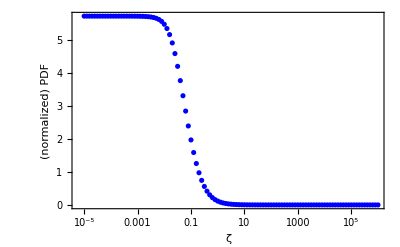

```mathematica
plotζFinalPDFPhaseLogNorm=ListLogLinearPlot[{ζFinalPDFPhaseLogNorm},PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue,Red},FrameLabel->{"ζ","(normalized) PDF"}]
```

#### Cumulative Distribution

Interpolation

```mathematica
ζFinalPDFPhaseInterpLogNorm=Interpolation[ζFinalPDFPhaseLogNorm];
```

Creating a table for cumulative distribution

```mathematica
ζFinalCDFPhaseNorm=Table[{ζSampleLog[[i]],NIntegrate[ζFinalPDFPhaseInterpLogNorm[x],{x,0,ζSampleLog[[i]]}]},{i,1,Length[ζSampleLog]}];
```

Plot

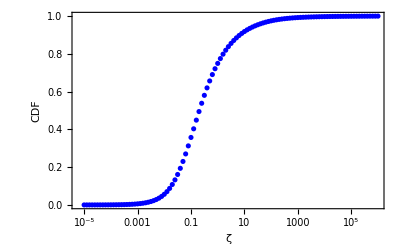

```mathematica
ListLogLinearPlot[ζFinalCDFPhaseNorm,PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue},FrameLabel->{"ζ","CDF"}]
```

CDF nicely asymptotes to 1 (suggesting that ζ = 100 is large enough)

#### Finding 90% credible limit for ζ

Interpolation for CDF

```mathematica
ζFinalCDFPhaseNormInterp=Interpolation[ζFinalCDFPhaseNorm]
```

InterpolatingFunction[…]

90% limit

```mathematica
ζ90CLphase=x/.FindRoot[ζFinalCDFPhaseNormInterp[x]==0.9,{x,0.02}]
```

6.65135

```mathematica
ζ  from amplitude correction
```

amplitude correction from ζ

```mathematica
𝒟logamp=HistogramDistribution[Log[ζampAll]] (*zeta from log of amp correction from monte-carlo*)
```

DataDistribution[…]

```mathematica
Histogram[Log[ζampAll]];
```

```mathematica
Histogram[ζampAll];
```

```mathematica
ps1amp=PDF[𝒟logamp,x];
ps2amp[x]=ps1amp;
```

```mathematica
MinLogζamp=Min[Log[ζampAll]]
```

-3.57242

```mathematica
MaxLogζamp=Max[Log[ζampAll]]
```

19.8127

```mathematica
plottestamp=Plot[ps2amp[x],{x,-5,20},Filling->Axis,PlotStyle->Gray];
```

```mathematica
Show[plottestamp,zeta1,Frame->True,PlotRange->All] ;(*Shows how much of the area under the curve satisfies zeta<1 from amplitude correction*)
```

```mathematica
Integrate[ps2amp[x],{x,Log[Min[ζampAll]],Log[Max[ζampAll]]}]
```

0.999674

```mathematica
Integrate[ps2amp[x],{x,Log[Min[ζampAll]],0}]/Integrate[ps2amp[x],{x,Log[Min[ζampAll]],Log[Max[ζampAll]]}]*100 (*59.3% area under the curve satisfies zeta<1 from amplitude correction*)
```

38.3168

```mathematica
ζSampleLogamp=Prepend[10^Range[-5,9,0.1],0];
```

```mathematica
fun1TableLogamp[y_]=Table[{ζSampleLogamp[[i]],fun1kent[ζSampleLogamp[[i]],y]},{i,1,Length[ζSampleLogamp]}];
```

```mathematica
ζMCamp[x_]=ps1amp;
```

```mathematica
ζMCamp[-5.5]
ζMCamp[19]
```

0.

0.0000612295

```mathematica
ζMCSampleamp=Range[-20,25,1.02];
```

```mathematica
ζMCTableamp=Table[{ζMCSampleamp[[i]],ζMCamp[ζMCSampleamp[[i]]]},{i,1,Length[ζMCSampleamp]}];
```

```mathematica
ζMCTableInterpamp=Interpolation[ζMCTableamp];
```

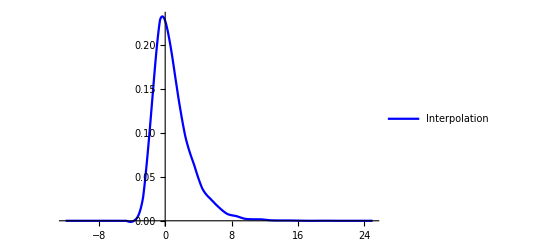

```mathematica
plotζMCTableInterpamp=Plot[ζMCTableInterpamp[x],{x,-12,25},PlotStyle->Blue,PlotLegends->{"Interpolation"},PlotRange->All]
```

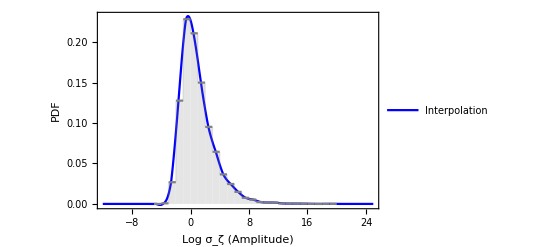

```mathematica
Show[plotζMCTableInterpamp,plottestamp,Frame->True,FrameLabel->{"Log σ_ζ (Amplitude)","PDF"}]
```

```mathematica
ζFinalPDFampLog=Table[{fun1TableLogamp[y][[i,1]],NIntegrate[fun1TableLogamp[y][[i,2]]ζMCTableInterpamp[y],{y,MinLogζamp,MaxLogζamp}]},{i,1,Length[fun1TableLogamp[y]]}];
```

```mathematica
ζFinalPDFampInterpLog=Interpolation[ζFinalPDFampLog];
```

Normalization

```mathematica
Normalizationζamp=NIntegrate[ζFinalPDFampInterpLog[x],{x,0,10^9}]
```

0.509778

```mathematica
ζFinalPDFampLogNorm=Table[{ζFinalPDFampLog[[i,1]],ζFinalPDFampLog[[i,2]]/Normalizationζamp},{i,1,Length[ζFinalPDFampLog]}];
```

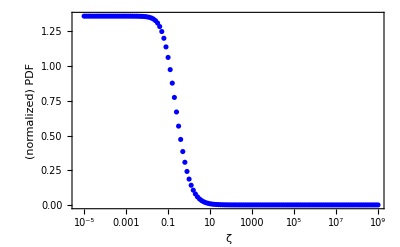

```mathematica
plotζFinalPDFampLogNorm=ListLogLinearPlot[{ζFinalPDFampLogNorm},PlotRange->Full,Frame->True,PlotStyle->{Blue,Red},FrameLabel->{"ζ","(normalized) PDF"}]
```

```mathematica
ζFinalPDFampInterpLogNorm=Interpolation[ζFinalPDFampLogNorm];
```

```mathematica
ζFinalCDFampNorm=Table[{ζSampleLogamp[[i]],NIntegrate[ζFinalPDFampInterpLogNorm[x],{x,0,ζSampleLogamp[[i]]}]},{i,1,Length[ζSampleLogamp]}];
```

```mathematica
ListLogLinearPlot[ζFinalCDFampNorm,PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue},FrameLabel->{"ζ","CDF"}];
```

```mathematica
ζFinalCDFampNormInterp=Interpolation[ζFinalCDFampNorm];
```

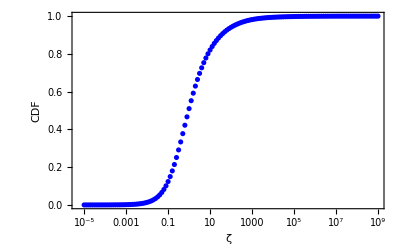

```mathematica
ListLogLinearPlot[ζFinalCDFampNorm,PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue},FrameLabel->{"ζ","CDF"}]
```

```mathematica
ζ90CLamp=x/.FindRoot[ζFinalCDFampNormInterp[x]==0.9,{x,12}]
```

34.0492

```mathematica
Combining the upper bounds on ζ from phase and amplitude corrections:
```

```mathematica
ζphaseAll
```

{0.851562,0.188078,0.0596121,504.343,2.43542,0.0222266,2.56208,0.125041,16317,0.0600925,0.10134,0.112184,0.124252,0.0200228,0.0372071,0.180842}
 |  |  |  |

```mathematica
ζampAll
```

{4.42067,0.986691,0.285816,2661.19,12.5834,0.0933842,13.6688,0.605417,16316,2.01686,0.290064,0.496736,0.54945,0.613411,0.0903926,0.166542,0.906687}
 |  |  |  |

```mathematica
ζcombined=(1/ζphaseAll^2+1/ζphaseAll^2)^(-1/2)
```

{0.602145,0.132991,0.0421521,356.624,1.7221,0.0157166,1.81166,0.0884174,16317,0.0424918,0.0716582,0.0793264,0.0878598,0.0141582,0.0263094,0.127874}
 |  |  |  |

```mathematica
𝒟logζcomb=HistogramDistribution[Log[ζcombined]]
```

DataDistribution[…]

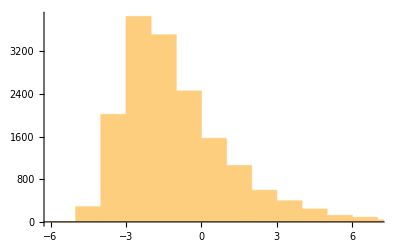

```mathematica
Histogram[Log[ζcombined]]
```

```mathematica
MinLogζcomb=Min[Log[ζcombined]]
```

-5.22094

```mathematica
MaxLogζcomb=Max[Log[ζcombined]]
```

17.7975

```mathematica
ps1ζcomb=PDF[𝒟logζcomb,x];
ps2ζcomb[x]=ps1ζcomb;
```

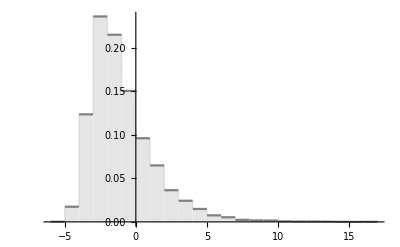

```mathematica
plotζcomb=Plot[ps2ζcomb[x],{x,-6,17},Filling->Axis,PlotStyle->Gray]
```

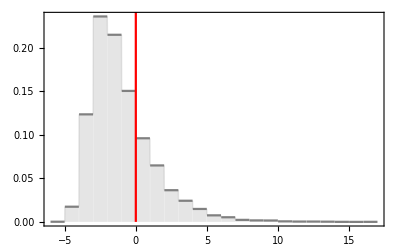

```mathematica
Show[plotζcomb,zeta1,Frame->True] (*Shows how much of the area under the curve satisfies zeta<1 from the combination of phase and amplitude*)
```

```mathematica
Integrate[ps2ζcomb[x],{x,MinLogζcomb,MaxLogζcomb}]
```

0.999844

```mathematica
Integrate[ps2ζcomb[x],{x,MinLogζcomb,0}]/Integrate[ps2ζcomb[x],{x,MinLogζcomb,MaxLogζcomb}]*100 (*89.7% area under the curve satisfies zeta<1 from amplitude correction*)
```

74.3054

```mathematica
ζSampleLogcomb=Prepend[10^Range[-5,5,0.1],0];
```

```mathematica
fun1TableLogcomb[y_]=Table[{ζSampleLogcomb[[i]],fun1kent[ζSampleLogamp[[i]],y]},{i,1,Length[ζSampleLogcomb]}];
```

```mathematica
ζMCcomb[x_]=ps1ζcomb;
```

```mathematica
ζMCcomb[-7.5]
ζMCcomb[17]
```

0.

0.0000612295

```mathematica
ζMCSamplecomb=Range[-8.5,17,1];
```

```mathematica
ζMCTablecomb=Table[{ζMCSamplecomb[[i]],ζMCcomb[ζMCSamplecomb[[i]]]},{i,1,Length[ζMCSamplecomb]}];
```

```mathematica
ζMCTableInterpcomb=Interpolation[ζMCTablecomb];
```

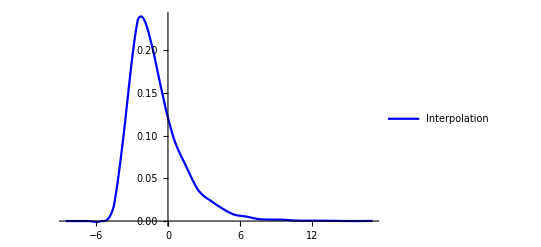

```mathematica
plotζMCTableInterpcomb=Plot[ζMCTableInterpcomb[x],{x,-8.5,17},PlotStyle->Blue,PlotLegends->{"Interpolation"},PlotRange->All]
```

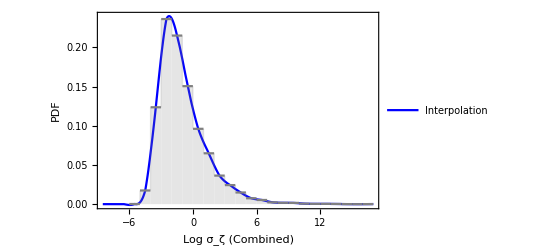

```mathematica
Show[plotζMCTableInterpcomb,plotζcomb,Frame->True,FrameLabel->{"Log σ_ζ (Combined)","PDF"}]
```

```mathematica
ζFinalPDFcombLog=Table[{fun1TableLogcomb[y][[i,1]],NIntegrate[fun1TableLogcomb[y][[i,2]]ζMCTableInterpcomb[y],{y,-8.5,17}]},{i,1,Length[fun1TableLogcomb[y]]}];
```

```mathematica
ζFinalPDFcombInterpLog=Interpolation[ζFinalPDFcombLog];
```

Normalization

```mathematica
Normalizationζcomb=NIntegrate[ζFinalPDFcombInterpLog[x],{x,0,10^5}]
```

0.499094

```mathematica
ζFinalPDFcombLogNorm=Table[{ζFinalPDFcombLog[[i,1]],ζFinalPDFcombLog[[i,2]]/Normalizationζcomb},{i,1,Length[ζFinalPDFcombLog]}];
```

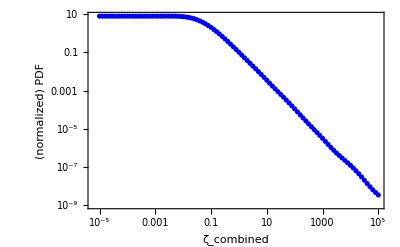

```mathematica
plotζFinalPDFcombLogNorm=ListLogLogPlot[{ζFinalPDFcombLogNorm},PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue,Red},FrameLabel->{"ζ_combined","(normalized) PDF"}]
```

```mathematica
ζFinalPDFcombInterpLogNorm=Interpolation[ζFinalPDFcombLogNorm]
```

InterpolatingFunction[…]

```mathematica
ζFinalCDFcombNorm=Table[{ζSampleLogcomb[[i]],NIntegrate[ζFinalPDFcombInterpLogNorm[x],{x,0,ζSampleLogcomb[[i]]}]},{i,1,Length[ζSampleLogcomb]}];
```

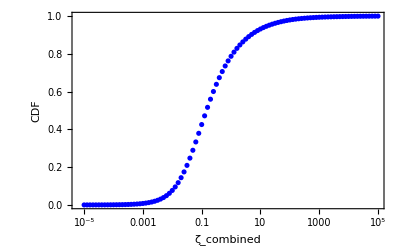

```mathematica
ListLogLinearPlot[ζFinalCDFcombNorm,PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue},FrameLabel->{"ζ_combined","CDF"}]
```

```mathematica
ζFinalCDFcombNormInterp=Interpolation[ζFinalCDFcombNorm];
```

```mathematica
ζ90CLcomb=x/.FindRoot[ζFinalCDFcombNormInterp[x]==0.9,{x,1}]
```

4.69066

```mathematica
Combining the upper bounds of Subscript[α^2, EDGB] from phase and amplitude corrections:
```

```mathematica
SquaredαEDGBcomb=(1/((SqrtαEDGBphase^4)^2)+1/((SqrtαEDGBamp^4)^2))^(-1/2)
```

{1.38555×10^6,322795.,99555.8,9.79784×10^8,3.70122×10^6,48551.2,5.48322×10^6,187384.,16316,847440.,96558.9,191202.,184116.,220219.,36954.1,74039.5,363441.}
 |  |  |  |

```mathematica
SqrtαEDGBphase^4
```

{1.41102×10^6,328606.,101698.,9.97224×10^8,3.7699×10^6,49907.4,5.57871×10^6,191339.,16316,865506.,98609.2,195141.,187914.,224691.,37849.8,75864.7,370599.}
 |  |  |  |

```mathematica
LogSquaredαcomb=Log[SquaredαEDGBcomb]
```

{14.1416,12.6848,11.5085,20.7028,15.1242,10.7904,15.5172,12.1409,16316,13.65,11.4779,12.1611,12.1233,12.3024,10.5174,11.2124,12.8034}
 |  |  |  |

```mathematica
Max[LogSquaredαcomb]
```

32.4962

```mathematica
Min[LogSquaredαcomb]
```

9.56973

```mathematica
𝒟logαcomb=HistogramDistribution[LogSquaredαcomb] ;
```

```mathematica
pslogαcomb=PDF[𝒟logαcomb,x];
```

```mathematica
Histogram[LogSquaredαcomb];
```

```mathematica
fun1αcomb[x_,y_]=1/(√(2*π)*Exp[y])*Exp[-x^2/(2Exp[2*y])] (*P(α^2|Subscript[σ, α^2])*)
```

(ⅇ^(-1/2 ⅇ^(-2 y) x^2-y))/(√(2 π))

```mathematica
αcombMC[x_]=pslogαcomb;
```

```mathematica
αcombMC[7]
```

0.

```mathematica
αcombMC[32]
```

0.0000612295

```mathematica
αMCSamplecomb=Range[6.5,32,1];
```

```mathematica
αMCTablecomb=Table[{αMCSamplecomb[[i]],αcombMC[αMCSamplecomb[[i]]]},{i,1,Length[αMCSamplecomb]}];
```

```mathematica
αMCTableInterpcomb=Interpolation[αMCTablecomb];
```

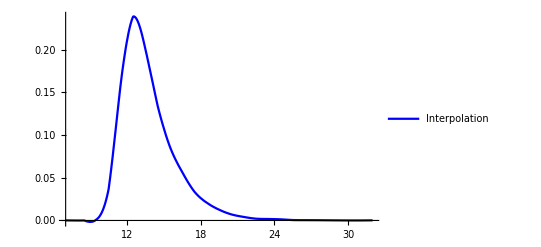

```mathematica
plotαMCTableInterpcomb=Plot[αMCTableInterpcomb[x],{x,7,32},PlotStyle->Blue,PlotLegends->{"Interpolation"},PlotRange->All]
```

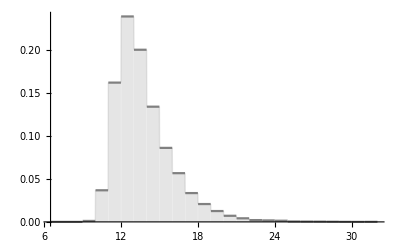

```mathematica
plot8=Plot[αcombMC[x],{x,6.5,32},Filling->Axis,PlotStyle->Gray,PlotRange->All]
```

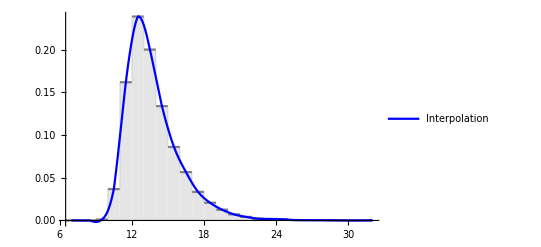

```mathematica
Show[plot8,plotαMCTableInterpcomb] (*Interpolation matches the actual pdf of monte-carlo*)
```

```mathematica
fun1αcombTable[y_]=Table[{αSampleLogamp[[i]],fun1αcomb[αSampleLogamp[[i]],y]},{i,1,Length[αSampleLogamp]}];
```

```mathematica
αFinalPDFcombLog=Table[{fun1αcombTable[y][[i,1]],NIntegrate[fun1αcombTable[y][[i,2]]αMCTableInterpcomb[y],{y,6.5,32}]},{i,1,Length[fun1αcombTable[y]]}];
```

```mathematica
αFinalPDFcombInterpLog=Interpolation[αFinalPDFcombLog]
```

InterpolatingFunction[…]

```mathematica
αNormalizationcomb=NIntegrate[αFinalPDFcombInterpLog[x],{x,0,10^15}]
```

0.499473

```mathematica
αFinalPDFcombLogNorm=Table[{αFinalPDFcombLog[[i,1]],αFinalPDFcombLog[[i,2]]/αNormalizationcomb},{i,1,Length[αFinalPDFcombLog]}];
```

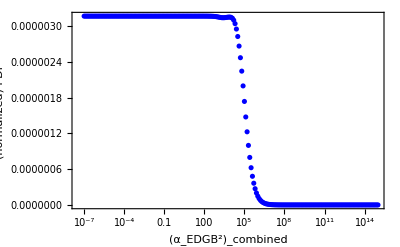

```mathematica
plotαFinalPDFcombLogNorm=ListLogLinearPlot[{αFinalPDFcombLogNorm},PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue,Red},FrameLabel->{"(α_EDGB^2)_combined","(normalized) PDF"}]
```

```mathematica
αFinalPDFcombInterpLogNorm=Interpolation[αFinalPDFcombLogNorm]
```

InterpolatingFunction[…]

```mathematica
αFinalCDFcombNorm=Table[{αSampleLogamp[[i]],NIntegrate[αFinalPDFcombInterpLogNorm[x],{x,0,αSampleLogamp[[i]]}]},{i,1,Length[αSampleLogamp]}];
```

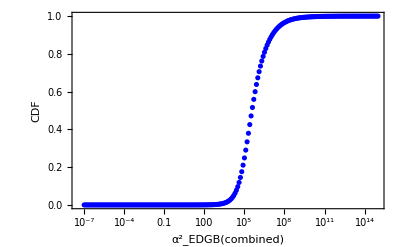

```mathematica
ListLogLinearPlot[αFinalCDFcombNorm,PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue},FrameLabel->{"α^2_EDGB(combined)","CDF"}]
```

```mathematica
αFinalCDFcombNormInterp=Interpolation[αFinalCDFcombNorm];
```

```mathematica
αSquared90CLcomb=x/.FindRoot[αFinalCDFcombNormInterp[x]==0.9,{x,100}](*90% CL of Subscript[α^2, EDGB] from phase correction *)
```

1.20222×10^7

```mathematica
√√αSquared90CLcomb
```

58.8838

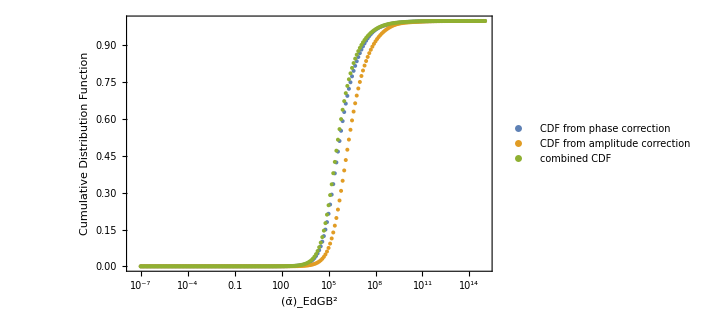

```mathematica
PlotCDFComparisonAll=ListLogLinearPlot[{αFinalCDFPhaseNorm,αFinalCDFampNorm,αFinalCDFcombNorm},PlotRange->All,TicksStyle->Directive["Label",14],AxesLabel->{nPN,Subscript[σ, α]},PlotLegends->{Placed[LineLegend[{"CDF from phase correction  ","CDF from amplitude correction","combined CDF"},LabelStyle->{FontSize->5},LegendMarkerSize->10,LegendMargins->0,LegendFunction->"Frame"],{Left,Top}]},FrameLabel->{"(ᾱ)_EdGB^2","Cumulative Distribution Function"},Frame->True]
```